```mathematica
Clear[Yalpha2,mN,Ms,xa,xb,xf,xi,gs,gstar,F];

mh=125;
mt=160;
mW=80.385;
GF=1.166378 10^-5;
v=1/Sqrt[Sqrt[2]*GF];
alphaem=1/128;
sw2=0.23129;

g=Sqrt[8/Sqrt[2] GF*mW^2];
gprime=Sqrt[(4 π *alphaem)/(1-sw2)];

yt=Sqrt[2]*(mt/v);

Mp=2.435*10^18;

hbar=6.58*10^(-25);
c=3*10^8;

kB=8.6173303 10^-5*10^-9 ; (* GeV/K*)
T0=kB*2.7255;
H0=(0.678 * hbar)/(9.777752 10^9 * 365.25*24*3600);
s0=4/3 π^2/30(2+21/11)T0^3;

lambda1=mh^2/v^2;
lambda2=3;
lambda3=9;
lambda4=0.01;
lambda5=-0.01;
l345=lambda3+lambda4+lambda5;

c1=(3*lambda1+2*lambda3+lambda4)/12+(3*g^2+gprime^2)/32+yt^2/8;
c2=(3*lambda2+2*lambda3+lambda4)/12+(3*g^2+gprime^2)/32;

(*Zero temp masses*)

mN=190;
Mspm=500;

muH2=lambda1*v^2;
mueta2=lambda3*v^2-2*Mspm^2;

meta2=Mspm^2+((lambda4+lambda5)/2)*v^2;
meta=Sqrt[meta2];

xf=xf; (*Freeze out of N???*)
Tf=mN/xf;

xa=(Sqrt[c2]*mN)/Sqrt[mueta2];
xb=Sqrt[(Sqrt[lambda2]*c1*mN^2-Sqrt[lambda1]*c2*mN^2)/(Sqrt[lambda2]*muH2-Sqrt[lambda1]*mueta2)];

Ta=mN/xa;
Tb=mN/xb;

Print[" xf = ",xf,"  xa = ",xa,"  xb = ",xb]
```

xf = xf  xa = 1.3476  xb = 4.08532

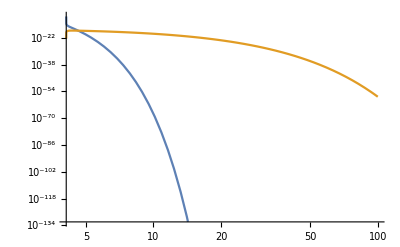

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

xa = 1.3476  xb = 4.08532  xfs = 4.40426  xi = 4.62296  xc = 113.723

Omega = 0.238354

```mathematica
Clear[Yalpha2,xi,xc,gs,gstar,F];

(*Mass in broken phase*)

veta2=(mueta2-c2*Tb^2)/lambda2;
meta2tb=lambda2*veta2;

gs=2;
gstarSM=106.75;
gstar=gstarSM+4+2*7/8;

s[x_]:=(2*Pi^2*gstar/45)*(mN/x)^3
H[x_]:=Sqrt[Pi^2*gstar/90]*(mN^2/(Mp*x^2));

sN=(2*Pi^2*gstar/45)*mN^3;
HN=Sqrt[Pi^2*gstar/90]*(mN^2/Mp);
sigmavN=(1/(4*Pi*mN^2))*Yalpha2^2;

lambda=(sN*sigmavN)/HN;

YN0=xf/lambda;

(*Depopulation Phase*)

m=0;

gN=2*7/8;
GammaN=(3*mN/(32*Sqrt[2]*Pi))*Yalpha2;

gx=gN;

Y1[x_]:=YN0*Exp[-(1/gN)*(GammaN/HN)*(x^2-xa^2)]/(1+lambda*YN0*((gN*HN)/(2*GammaN))*(1/xa^3-Exp[-(1/gN)*(GammaN/HN)*(x^2-xa^2)]/x^3));

(*Regeneration Phase*)

sigmavs=(gprime^4+3*g^4+g^2*gprime^2)/(128*Pi*Ms^2);
lambdas=(sN*sigmavs)/HN;

GammaS=(meta/(16*Pi))*Yalpha2*(1-mN^2/meta^2)^2;

Yxeq[x_]:=(45/(2*Pi^4))*(Pi/8)^(1/2)*(gx/gstar)*x^(3/2)*Exp[-x];
Yseq[x_]:=(45/(2*Pi^4))*(Pi/8)^(1/2)*(gs/gstar)*x^(3/2)*Exp[-x];

Yxxb=0;
YSxb=(Sqrt[meta2tb/meta2])^(3/2)*Exp[(Sqrt[meta2]-Sqrt[meta2tb])/Tb]*Yseq[xb];

YS[x_]:=YSxb*Exp[-GammaS/(gs*HN)*(x^2-xb^2)]/(1+((gs*HN*lambdas*YSxb)/(2*GammaS))*(1/xb^3-Exp[-(GammaS/(gs*HN))*(x^2-xb^2)]/x^3));

mx=mN;
ms=meta;
Ms=meta;

Yx[x_]:=Yxxb+((YS[xb]*Exp[(GammaS*xb^2)/(2*HN)])/(GammaS+lambdas*HN*YS[xb]))*Sqrt[(Pi*HN*GammaS)/2]*(Erf[Sqrt[GammaS/(2*HN)]*x]-Erf[Sqrt[GammaS/(2*HN)]*xb]);

Yalpha2=2*10^-14;  (*Change here*)

LogLogPlot[{H[x],sigmavs*s[x]*YS[x]},{x,1,100}];
LogLogPlot[{YS[x],Yseq[x]},{x,xb,100}];
LogLogPlot[{YS[x]*Yxeq[x],Yx[x]*Yseq[x]},{x,xb,100}]

xfs=x/.FindRoot[H[x]-sigmavs*s[x]*YS[x]==0,{x,4.5}];
xc=x/.FindRoot[YS[x]-Yseq[x]==0,{x,10}];
xi=x/.FindRoot[YS[x]*Yxeq[x]-Yx[x]*Yseq[x]==0,{x,4.5}];

Print["xa = ",xa,"  xb = ",xb,"  xfs = ",xfs,"  xi = ",xi,"  xc = ",xc]

Yxi=YS[xi]*(1+(mx/ms)^(3/2)*Exp[xi*(ms-mx)/mx]);

Yinf1=Yxi;
Yinf2=Yxi/(1+(lambdas/2)*(ms/mx)^3*(mx/(ms-mx))*Yxi*Exp[-2*xi*(ms-mx)/mx]/xi^(2+m));

F=1.45;

OmegaN1=(mN*s0*Yinf1)/(3*H0^2*Mp^2*F);
OmegaN2=(mN*s0*Yinf2)/(3*H0^2*Mp^2*F);

Print["Omega = ",OmegaN1]

sol=NDSolve[{YS'[x]==-(GammaS*x/HN)*(Ys\S[x]-(Yx[x]/Yxeq[x])*Yseq[x])-(lambdas/x^(m+2))*(YS[x]+Yseq[x])*(YS[x]-Yseq[x]),Yx'[x]==(GammaS*x/HN)*(Ys[x]-(Yx[x]/Yxeq[x])*Yseq[x]),Yx[xb]==0,Ys[xb]==(Sqrt[meta2tb/meta2])^(3/2)*Exp[(Sqrt[meta2]-Sqrt[meta2tb])/Tb]*Yseq[xb]},{Ys,Yx},{x,xb,30}];

LogLogPlot[{Ys[x]/.sol[[1,1]],Yseq[x]},{x,xb,5}]
LogLogPlot[{(Ys[x]/.sol[[1,1]])*Yxeq[x],(Yx[x]/.sol[[1,2]])*Yseq[x]},{x,xb,20}]
LogLogPlot[{Yx[x]/.sol[[1,2]],Yxeq[x]},{x,xb,30}]
```